```mathematica
Quit[];
```

Change Log: 
Version 2
16.10.2017
1. successfully implemented NDSolver to 83 steps
v 2.1
24.10.2017
** inserted save function to save the global variables, so that i can load the data from a file instead of calculating afresh every time.
v 2.2
28.5.2018
1. Implemented initialization cells
2. used shuttling-time variable(removed due to problems)
3. Calculated Quanta vs time graph
v2.3
1. changed strip width to 15 um
2. saved Data to file v2.3.nb.wl
3. calculated Y-motion of ion Plot
4. Calculated ion height vs Secular freq Plot
5. Calculated ion height vs trap depth Plot
v2.3.1
1. Changed sep from 5um to 0um (made it gapeless)
v2.3.2
1. Changed step from 20us to 20ms (it took too much time .. abandoned)
v2.3.3.1
1. Changed step from 20ms to 10us
2. replaced with new stripdata with maximum (a+b=26) electrode
na=3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,5,5,5,5,5,5,5,5,5,5,5,5,5,5,7,7,7,7,7,7,7,9,9,9
nb=6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,11,12,13,14,15,16,17,18,19,20,21,22,23,24,16,17,18,19,20,21,22,18,19,20
3. changed tt2 to 40 step(last two steps are same)
4. AccuracyGoal→5,MaxSteps→Infinity,PrecisionGoal→5,NormFunction→ Infinity
5. Calculate Total cycles of ion vibration

## Save function to save the global variables, so that i can load the data from a file instead of calculating afresh every time.

Create a file name

```mathematica
$LocalBase
```

file:///home/channayousif/.Wolfram/Objects

```mathematica
tmpfile=FileNameJoin[{$LocalBase,"vv.wl"}];
```

```mathematica
tmpfile
```

file:/home/channayousif/.Wolfram/Objects/vv.wl

Delete an old file

```mathematica
DeleteFile[SystemDialogInput["FileOpen",tmpfile]
```

Save file

```mathematica
Save[SystemDialogInput["FileSave",tmpfile],nDSS]//Timing
EmitSound[Sound[SoundNote[]]]
```

{518.586,Null}

Load file

```mathematica
Get[SystemDialogInput["FileOpen",tmpfile]]//Timing
EmitSound[Sound[SoundNote[]]]
```

{503.54,{37798.6,{{x→InterpolatingFunction[{{0., 0.0016}}, <>],y→InterpolatingFunction[{{0., 0.0016}}, <>],z→InterpolatingFunction[{{0., 0.0016}}, <>]}}}}

## Define constants

```mathematica
e = 1.6 10^-19;
my = 171 1.66 10^-27;
Ω = 2 π 15000000;
ψ = (e^2) / (4 my Ω^2);

eps=8.854 10^-12;
```

## (*Variables*)

```mathematica
(*sigma=b/a;*)
(*depth geometric factor kappa can be maximised for equal width rf electrodes (b=c) when the ratio between rf width and separation sigma≈3.68 and h≈1.43a (Altaf Separation)*)
(*a=b/sigma;*)

Vrf=200;         (* RF voltage in volts*)
(*Z=1000;       *)   (* Length of RF electrodes in z-axes should be very large -> Infinity*)
width=15 10^-6;(* 15um *)
sep=0 10^-6; (* Gapeless*)
(*amax=40 10^-6;
bmax=600 10^-6;
x1=amax/2;*)
(*x2=width;*)
z1=-1000;
z2=1000;
m=1; (*coefficient factor to set time for each step higher value indicates slow shift from one state to another*)
step=10 10^-6;
(*shuttlingtime=5step; Problematic *)(*duration in which ion is vertically shutteled it is from 0 to 83step *)
```

## Data of Electrodes to turn on

```mathematica
naa={3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,5,5,5,5,5,5,5,5,5,5,5,5,5,5,7,7,7,7,7,7,7,9,9,9};
nbb={6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,11,12,13,14,15,16,17,18,19,20,21,22,23,24,16,17,18,19,20,21,22,18,19,20};
```

```mathematica
na[t_]:=Indexed[naa,Ceiling[(10^-12)+(t)/step]];
nb[t_]:=Indexed[nbb,Ceiling[(10^-12)+(t)/step]];
```

```mathematica
Show[%,PlotRange-> {{0,3step},{0,10}}]
```

```mathematica
a[t_]:=na[t](width+sep)+sep;
b[t_]:=nb[t] (width+sep)-sep;
c[t_]:= nb[t] (width+sep)-sep;
widtht[t_]:={nb[t](width+sep)+width};
```

## Check point

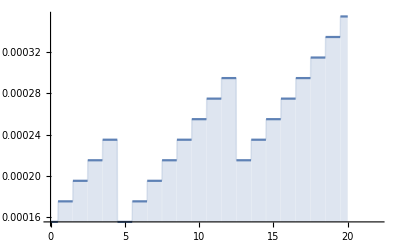

```mathematica
Plot[widtht[t step],{t,0,22},Filling->Bottom]
```

```mathematica
nb[100step]
```

40

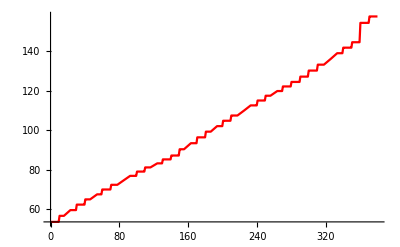

```mathematica
Plot[yp[t*10^-6 ]/10^-6,{t,0,tt2/10^-6},MaxRecursion->3,PlotStyle->Red]
```

## Define RF function

```mathematica
rffx[x_,y_,z_,t_,n_]:=Vrf/(2π)(
ArcTan[((a[t]/2+widtht[t]+(n-1)(width+sep)-x)(z2-z))/(y√(y^2+(a[t]/2+widtht[t]+(n-1)(width+sep)-x)^2+(z2-z)^2))]-ArcTan[((a[t]/2+(n-1)(width+sep)-x)(z2-z))/(y√(y^2+(a[t]/2+(n-1)(width+sep)-x)^2+(z2-z)^2))]- ArcTan[((a[t]/2+widtht[t]+(n-1)(width+sep)-x)(z1-z))/(y√(y^2+(a[t]/2+widtht[t]+(n-1)(width+sep)-x)^2+(z1-z)^2))]+ ArcTan[((a[t]/2+(n-1)(width+sep)-x)(z1-z))/(y√(y^2+(a[t]/2+(n-1)(width+sep)-x)^2+(z1-z)^2))])Cos[Ω ]+
-Vrf/(2π)(
ArcTan[((a[t]/2-a[t]-widtht[t]-(n-1)(width+sep)-x)(z2-z))/(y√(y^2+(a[t]/2-a[t]-widtht[t]-(n-1)(width+sep)-x)^2+(z2-z)^2))]-ArcTan[((a[t]/2-a[t]-(n-1)(width+sep)-x)(z2-z))/(y√(y^2+(a[t]/2-a[t]-(n-1)(width+sep)-x)^2+(z2-z)^2))]- ArcTan[((a[t]/2-a[t]-widtht[t]-(n-1)(width+sep)-x)(z1-z))/(y√(y^2+(a[t]/2-a[t]-widtht[t]-(n-1)(width+sep)-x)^2+(z1-z)^2))]+ArcTan[((a[t]/2-a[t]-(n-1)(width+sep)-x)(z1-z))/(y√(y^2+(a[t]/2-a[t]-(n-1)(width+sep)-x)^2+(z1-z)^2))])Cos[Ω ]
rffxt[x_,y_,z_,t_]:=rffx[x,y,z,t,1];
```

Check point

```mathematica
Manipulate[Plot3D[ϕ1[x,ys,0,t],{x,- 80step,80step},{t,0,100 20 10^-6},AxesLabel->Automatic,PlotRange->Full],{ys,step,50step}];
```

```mathematica
Manipulate[Plot[rffxt[x,step,step,t],{x,- 80step,80step},PlotRange->Full],{t,0,200step}];
```

## Define Trap

```mathematica
trap[x_,y_,z_,t_]:=rffxt[x,y,z,t];
ϕ1[x_,y_,z_,t_]:={
Block[{x11,y11,z11,t0:=t},{
rfelectrodesVar[x11,y11,z11]=trap[x11,y11,z11,t0];
temp[x11,y11,z11]=ψ(D[rfelectrodesVar[x11,y11,z11],x11]^2 +D[rfelectrodesVar[x11,y11,z11],y11]^2 +D[rfelectrodesVar[x11,y11,z11],z11]^2)}];
temp[x11,y11,z11]/.{x11->x,y11->y,z11->z}
};
```

```mathematica
sigma[t_]:=b[t]/a[t];
yP[t_]:=(a[t] b[t] c[t](a[t]+b[t]+c[t]))^0.5/(b[t]+c[t]);
yE[t_]:=√(2 a[t] b[t]+a[t]^2+2(a[t]+b[t])√(2a[t] b[t]+a[t]^2))/2;
Xnill[t_]:=0;
```

### Check point ..

```mathematica
ϕ1[0,step,0,step]
```

{1.61574×10^-17}

```mathematica
Plot[na[n step],{n,0,83}];
```

```mathematica
ContourPlot[ϕ1[x,y,0,step]/e,{x,-(a[step] +0b[step]),(a[step] +0.001b[step])},{y,yP[step]-.5step,yE[step]}];
```

```mathematica
ContourPlot[ϕ1[x,y,0,5step]/e, {x,-1.5step,1.5step},{y,yP[5step]-.5step,yE[5step]+step},Contours->10];
```

```mathematica
Plot[{ϕ1[0,y,0,1step]/e,ϕ1[0,y,0,2step]/e,ϕ1[0,y,0,3step]/e,ϕ1[0,y,0,4step]/e,ϕ1[0,y,0,4step]/e},{y,step,10step}];
```

```mathematica
Manipulate[Plot[trap[x,.000002,0,nn step],{x,-(a[nn step]+b[nn step]),(a[nn step]+b[nn step])},PlotRange->All],{nn ,0,48,1}];
```

```mathematica
Plot[{0a[tt],0b[tt],0na[tt],0nb[tt],0Xnill[tt],0sigma[tt],yP[tt],0yE[tt]},{tt,0,83step}]
```

## Trap Depth check with first derivative method..

```mathematica
zz=0.000000;   (* cross-section point *)
xx[t_]=Xnill[t];
yy[t_]=yP[t];  (* ?? yE=0.0002*)
```

```mathematica
Clear[tt,yp,xp,zp]
```

```mathematica
dervX[x_,y_,z_,tt_](*:=dervX[x,y,z,tt]*)= {Block[{x11,y11,z11},tmp1[x11,y11,z11]=D[ ϕ1[x11,y11,z11,tt],x11]];tmp1[x11,y11,z11]/.{x11->x,y11->y,z11->z}};
dervY[x_,y_,z_,tt_](*:=dervY[x,y,z,tt]*)= {Block[{x11,y11,z11},tmp2[x11,y11,z11]=D[ ϕ1[x11,y11,z11,tt],y11]];tmp2[x11,y11,z11]/.{x11->x,y11->y,z11->z}};
dervZ[x_,y_,z_,tt_](*:=dervZ[x,y,z,tt]*)= {Block[{x11,y11,z11},tmp3[x11,y11,z11]=D[ ϕ1[x11,y11,z11,tt],z11]];tmp3[x11,y11,z11]/.{x11->x,y11->y,z11->z}};
```

```mathematica
(*dervY[x_,y_,z_] = D[ ϕ1[x,y,z,tt],y];
dervZ[x_,y_,z_] = D[ ϕ1[x,y,z,tt],z];*)
xp[tt_]:=xp[tt]=x/.FindRoot[{dervX[x,y,z,tt]==0,dervY[x,y,z,tt]==0,dervZ[x,y,z,tt]==0},{{x,xx[tt]},{y,Evaluate[yy[tt]]},{z,zz}}];
yp[tt_]:=yp[tt]=y/.FindRoot[{dervX[x,y,z,tt]==0,dervY[x,y,z,tt]==0,dervZ[x,y,z,tt]==0},{{x,xx[tt]},{y,Evaluate[yy[tt]]},{z,zz}}];
zp[tt_]:=zp[tt]=z/.FindRoot[{dervX[x,y,z,tt]==0,dervY[x,y,z,tt]==0,dervZ[x,y,z,tt]==0},{{x,xx[tt]},{y,Evaluate[yy[tt]]},{z,zz}}];
ye[tt_]:=ye[tt]=y/.FindRoot[{dervX[x,y,z,tt]==0,dervY[x,y,z,tt]==0,dervZ[x,y,z,tt]==0},{{x,xx[tt]},{y,Evaluate[yE[tt]]},{z,zz}}];
ze[tt_]:=ze[tt]=z/.FindRoot[{dervX[x,y,z,tt]==0,dervY[x,y,z,tt]==0,dervZ[x,y,z,tt]==0},{{x,xx[tt]},{y,Evaluate[yy[tt]]},{z,zz}}];
TddY[tt_]:=TddY[tt]=( ϕ1[xx[tt],ye[tt],zz,tt]- ϕ1[xx[tt],yp[tt],zz,tt])/e;

(*Print["Trap Depth in Z-axes= ",TddZ=( ϕ[xx,yy,zz+0.0003]- ϕ[xx,yy,0])/e]*)
```

### Check point

```mathematica
TableForm[
{
Show[
{

},
{t,0,83},
ImageSize->Medium,
PlotRange->All,
PlotStyle->Thick,
PlotLabels->{"asd","ssd"},
Frame->True,
FrameLabel->"plot description here",
AxesLabel->{x,y},
PlotLabel->"Plot name here",
LabelStyle->Directive[Bold,Orange]],
"Settings: \n Width of single Rf strip=15um \n separation=5um \n Time step=20 us"
}
]
```

-Graphics-
Settings: 
 Width of single Rf strip=15um 
 separation=5um 
 Time step=20 us

```mathematica
(*xp[tt_]:=xp[tt]=x/.FindRoot[{D[ ϕ1[x,y,z,tt],x]==0,D[ ϕ1[x,y,z,tt],y]==0,D[ ϕ1[x,y,z,tt],z]==0},{{x,Evaluate[xx[tt]]},{y,Evaluate[yy[tt]]},{z,zz}}];
yp[tt_]:=yp[tt]=y/.FindRoot[{D[ ϕ1[x,y,z,tt],x]==0,D[ ϕ1[x,y,z,tt],y]==0,D[ ϕ1[x,y,z,tt],z]==0},{{x,Evaluate[xx[tt]]},{y,Evaluate[yy[tt]]},{z,zz}}];
zp[tt_]:=zp[tt]=z/.FindRoot[{D[ ϕ1[x,y,z,tt],x]==0,D[ ϕ1[x,y,z,tt],y]==0,D[ ϕ1[x,y,z,tt],z]==0},{{x,Evaluate[xx[tt]]},{y,Evaluate[yy[tt]]},{z,zz}}];
ye[tt_]:=ye[tt]=y/.FindRoot[{D[ ϕ1[x,y,z,tt],x]==0,D[ ϕ1[x,y,z,tt],y]==0,D[ ϕ1[x,y,z,tt],z]==0},{{x,Evaluate[xx[tt]]},{y,Evaluate[yE[tt]]},{z,zz}}];*)
```

```mathematica
(*Print["Z_Secular = ",√(derv2Z[xp,yp,zp]/my)/(2 π)] *)
```

## NDSolver

```mathematica
TotalP[x_,y_,z_,t_]:=ϕ1[x,y,z,t];
```

```mathematica
xp[0]=0;
yp[0];
zp[0];
h=6.63 10^(-34)/2 Pi;
tt1=0step;
tt2=38 step;
```

```mathematica
starttime=Now
nDSS=NDSolve[{
my x''[t]+D[ϕ1[x[t],y[t],z[t],t], x[t]]==0,
my y''[t]+D[ϕ1[x[t],y[t],z[t],t], y[t]]==0,
my z''[t]+D[ϕ1[x[t],y[t],z[t],t], z[t]]==0,
x'[0]==0,
y'[0]==0,
z'[0]==0,
x[0]==xp[0],
y[0]==yp[0],
z[0]==zp[0]},
{x,y,z},{t,tt1,tt2},AccuracyGoal->5,MaxSteps->Infinity,PrecisionGoal->5,NormFunction-> Infinity,Method->{"StiffnessSwitching",Method->{"ExplicitRungeKutta",Automatic}}]//Timing
endtime=Now
```

Tue 25 Sep 2018 19:25:53GMT

Indexed::partw: Part 40 of {3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,5,5,5,5,5,5,5,5,5,5,5,5,5,5,7,7,7,7,7,7,7,9,9,9} does not exist.

Indexed::partw: Part 40 of {6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,11,12,13,14,15,16,17,18,19,20,21,22,23,24,16,17,18,19,20,21,22,18,19,20} does not exist.

Indexed::partw: Part 40 of {3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,7.,7.,7.,7.,7.,7.,7.,9.,9.,9.} does not exist.

General::stop: Further output of Indexed::partw will be suppressed during this calculation.

NDSolve::nlnum: The function value «1» is not a list of numbers with dimensions {6} at {t,x[t],x'[t],y[t],y'[t],z[t],z'[t],NDSolve`s$13333[t]} = {0.00039,0.,0.,0.000176254,-177.189,6.48997×10^-38,3.59826×10^-34,79}.

{5582.3,{{x→InterpolatingFunction[{{0., 0.00039}}, <>],y→InterpolatingFunction[{{0., 0.00039}}, <>],z→InterpolatingFunction[{{0., 0.00039}}, <>]}}}

Tue 25 Sep 2018 20:58:58GMT

```mathematica
nD= Last[nDSS];
tstart=First[First[First[First[y/.nD]]]];
timelimit=Last[First[First[First[y/.nD]]]]
```

0.00039

Trap Depth

```mathematica
TdY[tt_]:=(ϕ1[Xnill[tt],ye[tt],0,tt]-ϕ1[Xnill[tt],yp[tt],0,tt])/e;
```

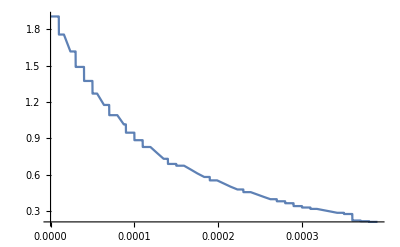

```mathematica
zxcv=Plot[TdY[tt],{tt,0,timelimit}]
```

```mathematica
TdY[step]
```

{{1.75698}}

```mathematica
tdvsy0=ParametricPlot[{First[First[TddY[t ]]],yp[t] 10^6 },{t,0,timelimit},PlotRange->All,AspectRatio->1/1.5]
```

ParametricPlot::plln: Limiting value timelimit in {t,0,timelimit} is not a machine-sized real number.

ParametricPlot[{First[First[TddY[t]]],yp[t] 10^6},{t,0,timelimit},PlotRange→All,AspectRatio→1/1.5]

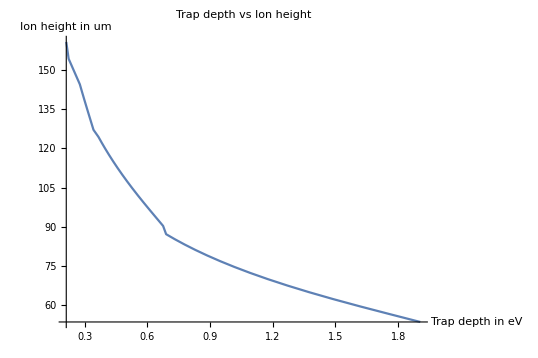

```mathematica
Show[tdvsy0,AxesLabel->{HoldForm[Trap depth in eV],HoldForm[Ion height in um]},PlotLabel->HoldForm[Trap depth vs Ion height],LabelStyle->{14,RGBColor[1.,0.,0.],Italic}]
```

```mathematica
Secular frequecies
(*Check with 2nd derivative method:;*)
```

```mathematica
tt=7step;
```

```mathematica
Clear[tt,Ysecf,derv2Y,derv2X,derv2Z]
```

```mathematica
pond2[x_,y_,z_,tt_]=ϕ1[x,y,z,tt]+ 0e test2[x,y,z]; (*pond2 = ϕ in case of rf only*)
(*derv2X[x_,y_,z_,tt_] := D[pond2[x,y,z,tt],{x,2}];
derv2Y[x_,y_,z_,tt_] := D[pond2[x,y,z,tt],{y,2}];
derv2Z[x_,y_,z_,tt_] := D[pond2[x,y,z,tt],{z,2}];*)
```

```mathematica
derv2X[x_,y_,z_,tt_]:={Block[{x11,y11,z11,t0:=tt},{
pond2t[x11,y11,z11]=pond2[x11,y11,z11,t0];
temp[x11,y11,z11]=D[pond2t[x11,y11,z11],{x11,2}];
temp[x11,y11,z11]/.{x11->x,y11->y,z11->z}}]};
derv2Y[x_,y_,z_,tt_]:={Block[{x11,y11,z11,t0:=tt},{
pond2t[x11,y11,z11]=pond2[x11,y11,z11,t0];
temp[x11,y11,z11]=D[pond2t[x11,y11,z11],{y11,2}];
temp[x11,y11,z11]/.{x11->x,y11->y,z11->z}}]};
derv2Z[x_,y_,z_,tt_]:={Block[{x11,y11,z11,t0:=tt},{
pond2t[x11,y11,z11]=pond2[x11,y11,z11,t0];
temp[x11,y11,z11]=D[pond2t[x11,y11,z11],{z11,2}];
temp[x11,y11,z11]/.{x11->x,y11->y,z11->z}}]};
Print["X_Secular = ",Xsecf[tt_]:=√(derv2X[xp[tt],yp[tt],zp[tt],tt]/my)/(2 π)];
Print["Y_Secular = ",Ysecf[tt_]:=√(derv2Y[xp[tt],yp[tt],zp[tt],tt]/my)/(2 π)];
```

X_Secular = Null

Y_Secular = Null

```mathematica
Ysecf[.0001]
```

{{{{6.14561×10^6}}}}

```mathematica
Plot[Ysecf[t ],{t,0step,timelimit}]
```

Plot::plln: Limiting value timelimit in {t,0,timelimit} is not a machine-sized real number.

Plot[Ysecf[t],{t,0 step,timelimit}]

```mathematica
Ysecfvsypt=ParametricPlot[{First[First[First[First[Ysecf[t ]]]]],yp[t ]10^6},{t,0,timelimit},AspectRatio->1/1.5]
```

ParametricPlot::plln: Limiting value timelimit in {t,0,timelimit} is not a machine-sized real number.

ParametricPlot[{First[First[First[First[Ysecf[t]]]]],yp[t] 10^6},{t,0,timelimit},AspectRatio→1/1.5]

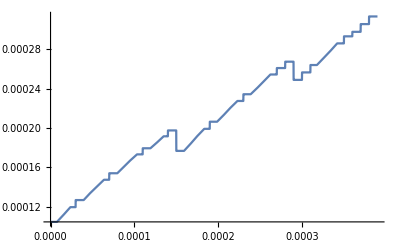

```mathematica
pye=Plot[ye[t],{t,0,timelimit}]
```

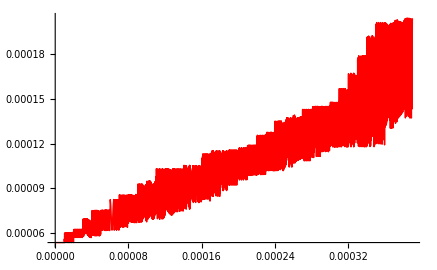

```mathematica
py=Plot[y[t]/.nD,{t,tstart,timelimit},PlotRange-> All,PlotStyle->{Thick, Red}]
```

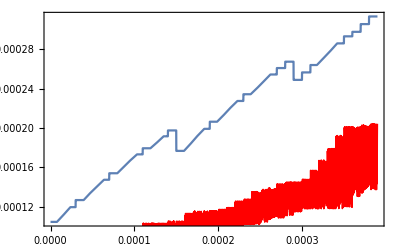

```mathematica
Show[pye,py,Frame->True,Origin-> {0,0}]
```

## Kinetic Energy & Potential:

```mathematica
KINE[t_]=(1/2 my ( (First[D[x[s], s]/.nD/.s-> t ])^2 + (First[D[y[s], s]/.nD/.s-> t])^2 +(First[D[z[s], s]/.nD/.s-> t ])^2 )/(e));
KINEx[t_]=(1/2 my ( (First[D[x[s], s]/.nD/.s-> t ])^2 )/(e));
KINEy[t_]=(1/2 my ( (First[D[y[s], s]/.nD/.s-> t ])^2 )/(e));
KINEz[t_]=(1/2 my ( (First[D[z[s], s]/.nD/.s-> t ])^2 )/(e));
```

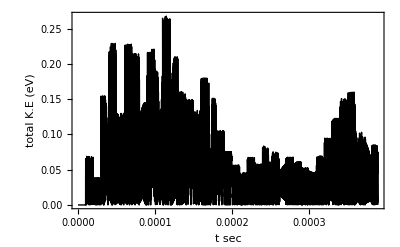

```mathematica
Plot[KINE[t],{t,tstart,timelimit},Frame-> True,PlotStyle->{Thin, Black},PlotRange->All,FrameStyle->Directive[Black,20,Bold],FrameLabel-> {"t sec","total K.E (eV)"}]
```

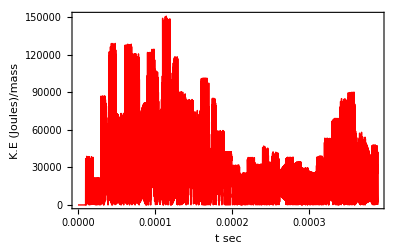

```mathematica
Plot[KINE[t]e/(my),{t,tstart,timelimit},Frame-> True,PlotStyle->{Thick, Red},PlotRange->All,FrameStyle->Directive[Black,20,Bold],FrameLabel-> {"t sec","K.E (Joules)/mass"}]
```

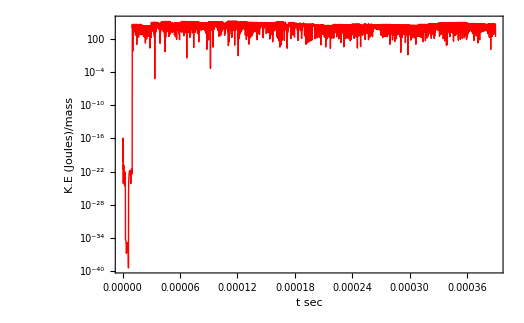

```mathematica
LogPlot[KINE[t]e/(my),{t,tstart,timelimit},Frame-> True,PlotStyle->{Thick, Red},PlotRange->All,FrameStyle->Directive[Black,20,Bold],FrameLabel-> {"t sec","K.E (Joules)/mass"}]
```

```mathematica
Print["   Peak Value TKE in Joules= ",Max[Table[{t,KINE[t] e},{t,tstart,timelimit,2 10^-6}]]];
```

Peak Value TKE in Joules= 0.00039

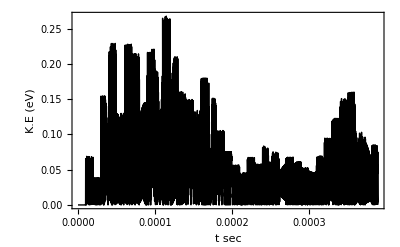

```mathematica
Plot[KINE[t],{t,tstart,timelimit},PlotRange-> All,Frame-> True,PlotStyle->{Thin, Black},PlotRange-> Full,FrameStyle->Directive[Black,20,Bold],FrameLabel-> {"t sec","K.E (eV)"}]
```

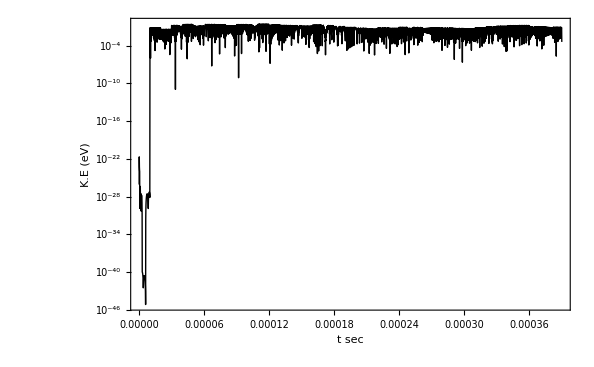

```mathematica
LogPlot[KINE[t],{t,tstart,timelimit},PlotRange-> All,Frame-> True,PlotStyle->{Thin, Black},PlotRange-> Full,FrameStyle->Directive[Black,20,Bold],FrameLabel-> {"t sec","K.E (eV)"}]
```

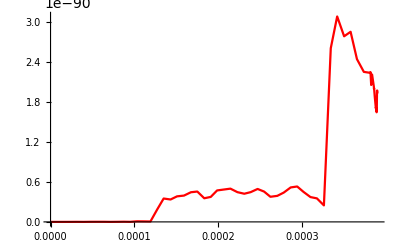

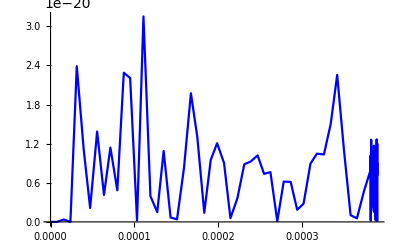

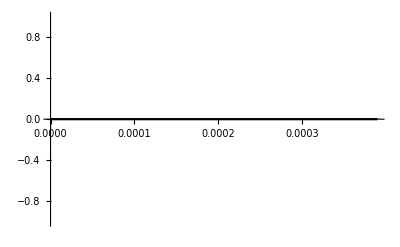

```mathematica
KEzmj=Plot[KINEz[t]e,{t,tstart,timelimit},PlotStyle-> Red,PlotRange-> All]

KEymj=Plot[KINEy[t]e,{t,tstart,timelimit},PlotStyle-> Blue,PlotRange-> All]

KExmj=Plot[KINEx[t]e,{t,tstart,timelimit},PlotStyle-> Black,PlotRange-> All]
```

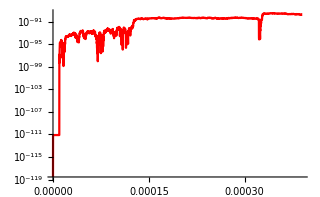

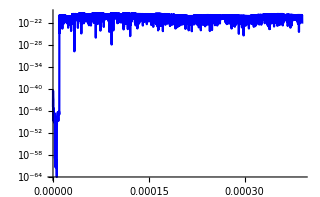

-Graphics-

```mathematica
KEzj=LogPlot[KINEz[t]e,{t,tstart,timelimit},PlotStyle-> Red,PlotRange-> All]

KEyj=LogPlot[KINEy[t]e,{t,tstart,timelimit},PlotStyle-> Blue,PlotRange-> All]

KExj=LogPlot[KINEx[t]e,{t,tstart,timelimit},PlotStyle-> Black,PlotRange-> All]
```

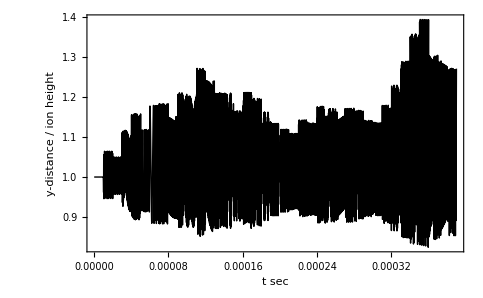

```mathematica
Plot[(y[t]/.nD)/yp[t],{t,0,timelimit},PlotRange-> All,Frame-> True,PlotStyle->{Thick, Black},PlotRange->All,FrameStyle->Directive[Black,22,Bold],FrameLabel-> {"t sec","y-distance / ion height"}]
```

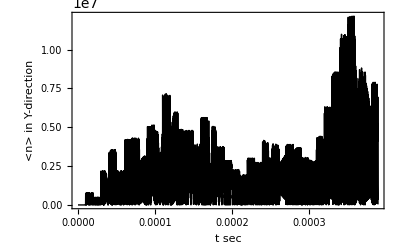

```mathematica
KEY=Plot[KINEy[t] e/(h Ysecf[t]),{t,tstart,timelimit},PlotRange-> All,Frame-> True,PlotStyle->{Thick, Black},FrameStyle->Directive[Black,22,Bold],FrameLabel-> {"t sec","<n> in Y-direction"}]
```

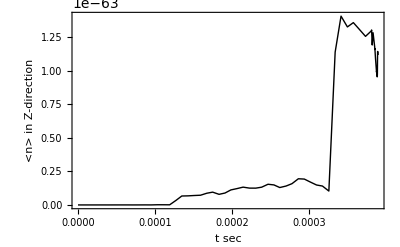

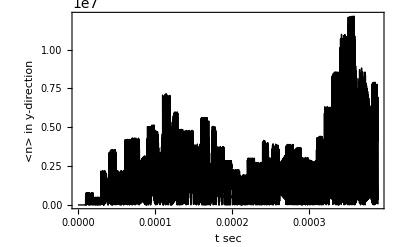

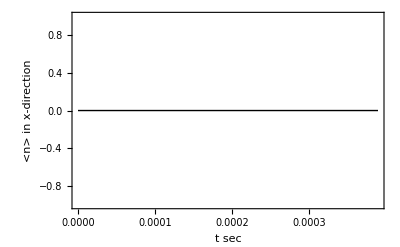

```mathematica
KEZm=Plot[KINEz[t] e/(h Ysecf[t]),{t,tstart,timelimit},Frame-> True,PlotStyle->{Thick, Black},PlotRange->All,FrameStyle->Directive[Black,22,Bold],FrameLabel-> {"t sec","<n> in Z-direction"}]
KEym=Plot[KINEy[t] e/(h Ysecf[t]),{t,tstart,timelimit},Frame-> True,PlotStyle->{Thick, Black},PlotRange->All,FrameStyle->Directive[Black,20,Bold],FrameLabel-> {"t sec","<n> in y-direction"}]
KExm=Plot[KINEx[t] e/(h Ysecf[t]),{t,tstart,timelimit},Frame-> True,PlotStyle->{Thick, Black},PlotRange->All,FrameStyle->Directive[Black,20,Bold],FrameLabel-> {"t sec","<n> in x-direction"}]
```

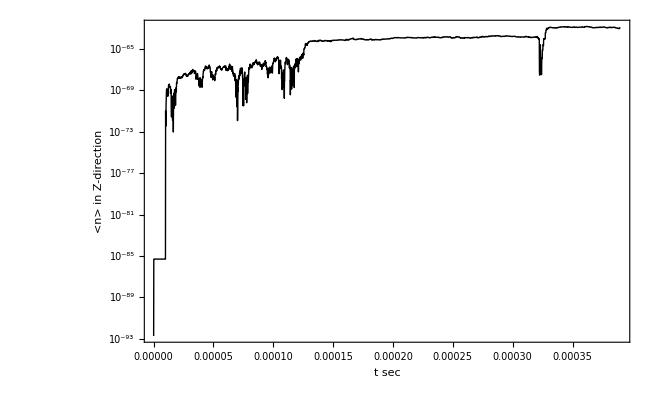

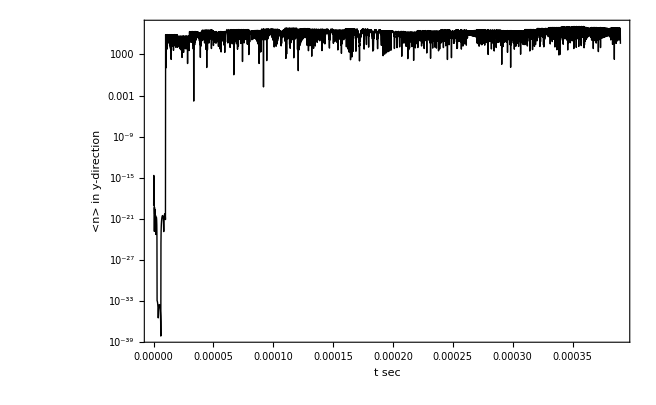

-Graphics-

```mathematica
KEZ=LogPlot[KINEz[t] e/(h Ysecf[t]),{t,tstart,timelimit},Frame-> True,PlotStyle->{Thick, Black},PlotRange->All,FrameStyle->Directive[Black,22,Bold],FrameLabel-> {"t sec","<n> in Z-direction"}]
KEy=LogPlot[KINEy[t] e/(h Ysecf[t]),{t,tstart,timelimit},Frame-> True,PlotStyle->{Thick, Black},PlotRange->All,FrameStyle->Directive[Black,20,Bold],FrameLabel-> {"t sec","<n> in y-direction"}]
KEx=LogPlot[KINEx[t] e/(h Ysecf[t]),{t,tstart,timelimit},Frame-> True,PlotStyle->{Thick, Black},PlotRange->All,FrameStyle->Directive[Black,20,Bold],FrameLabel-> {"t sec","<n> in x-direction"}]
```

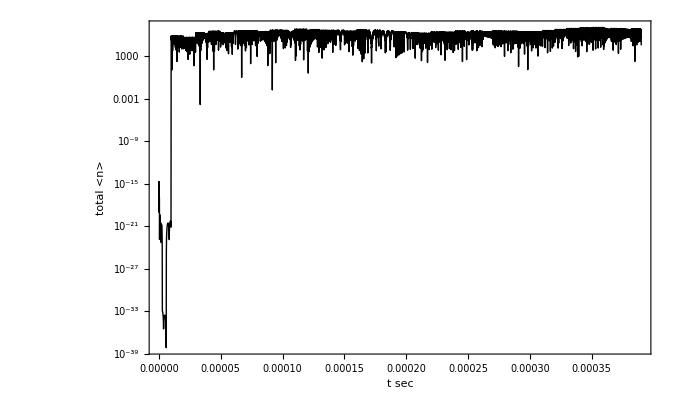

```mathematica
LogPlot[KINE[t] e/(h Ysecf[t]),{t,tstart,timelimit},Frame-> True,PlotStyle->{Thick, Black},PlotRange->All,FrameStyle->Directive[Black,22,Bold],FrameLabel-> {"t sec","total <n> "}]
```

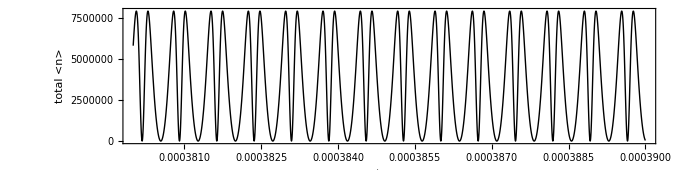

```mathematica
Plot[KINE[t] e/(h Ysecf[t]),{t,timelimit-step,timelimit},Frame-> True,PlotStyle->{Thick, Black},PlotRange->All,FrameStyle->Directive[Black,22,Bold], FrameLabel-> {"t sec","total <n> "},AspectRatio->1/4]
```

```mathematica
keEnd=Max[Table[KINE[t],{t,timelimit-.1step,timelimit,10^-9}]]
```

0.0853622

```mathematica
keStart=Max[Table[KINE[t],{t,0,.2step,10^-9}]]
```

1.20192×10^-20

```mathematica
Print["< n > = ",avrN=keEnd e/(h  Ysecf[timelimit-0.1step])-keStart e/(h  Ysecf[0.2step])]
```

< n > = {{{{7.90395×10^6}}}}

```mathematica
Print["< nE > = ",avrN=(keEnd-0)e/(h  Ysecf[timelimit-0.0000001])]
```

< nE > = {{{{7.90395×10^6}}}}

```mathematica
timelimit
```

0.00039

```mathematica
numcycles=First[First[First[First[Sum[Ysecf[t] step,{t,0,timelimit,step}]]]]]
```

2011.83

```mathematica
Mean[Table[Ysecf[t],{t,0,timelimit,.25step}]]
```

{{{{5.09397×10^6}}}}

```mathematica
secf=Table[Ysecf[t step] step,{t,0,timelimit/step,1}]
```

{{{{{149.331}}}},{{{{133.415}}}},{{{{119.963}}}},{{{{108.524}}}},{{{{98.7287}}}},{{{{90.2805}}}},{{{{82.9433}}}},{{{{76.529}}}},{{{{70.8869}}}},{{{{65.8955}}}},{{{{61.4561}}}},{{{{57.4882}}}},{{{{53.9254}}}},{{{{50.7127}}}},{{{{47.8043}}}},{{{{52.5336}}}},{{{{49.0987}}}},{{{{45.9956}}}},{{{{43.1867}}}},{{{{40.6381}}}},{{{{38.3198}}}},{{{{36.2057}}}},{{{{34.2728}}}},{{{{32.501}}}},{{{{30.8728}}}},{{{{29.3731}}}},{{{{27.9885}}}},{{{{26.7073}}}},{{{{25.5193}}}},{{{{26.5413}}}},{{{{25.2899}}}},{{{{24.1262}}}},{{{{23.0432}}}},{{{{22.034}}}},{{{{21.0926}}}},{{{{20.2132}}}},{{{{17.9517}}}},{{{{17.2525}}}},{{{{16.5923}}}},{{{{16.5923}}}}}

```mathematica
16.5923/step
```

1.65923×10^6

```mathematica
ArrayDepth[{{{{5.072226566883917*^6}}}}]
```

4

```mathematica
numcycles
```

2011.83

```mathematica
cycles[t_]:=((t)/timelimit);
```

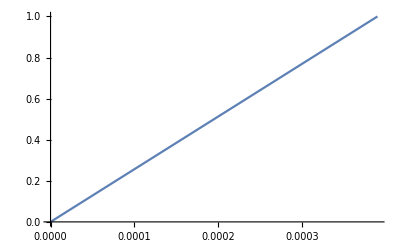

```mathematica
Plot[cycles[t],{t,0,timelimit}]
```

```mathematica
Plot[KINE[cycles[t]/Ysecf[t]] e/(h Ysecf[t]),{t,timelimit-step,timelimit},Frame-> True,PlotStyle->{Thick, Black},PlotRange->All,FrameStyle->Directive[Black,22,Bold],FrameLabel-> {"T ω/2π","total <n> "}]
```

```mathematica
KINEy[t/Ysecf[t]] e/(h Ysecf[t]),{t,timelimit-step,timelimit}
```

```mathematica
NMaxEnd=Max[Table[KINEy[t/Ysecf[t]] e/(h Ysecf[t]),{t,timelimit-step,timelimit}]]
NMaxStart=Max[Table[KINEy[t/Ysecf[t]] e/(h Ysecf[t]),{t,0,step,0.000001}]]
NMaxEnd-NMaxStart
```

6.81934×10^-16

8.65002×10^-22

6.81933×10^-16

```mathematica
NMax=Max[Table[KINE[t/Ysecf[t]] e/(h Ysecf[t]),{t,timelimit-step,timelimit,0.000001}]]
NMin=Max[Table[KINE[t/Ysecf[t]] e/(h Ysecf[t]),{t,0,step,0.000001}]]
NMax-NMin
```

7.173×10^-16

8.65002×10^-22

7.17299×10^-16